```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../"];
SetOptions[NDSolve, AccuracyGoal-> 13, PrecisionGoal-> 13, 
Compiled-> False, MaxSteps-> Infinity];
<<"NLink`";
SetDirectory[NotebookDirectory[]];
```

```mathematica
np = 1; (* # of puppeteers *)
nl = 0; (* # of links *)
n = np + nl; (* # of bodies *)
(* puppeteer (wheel + winch) *)

R = 1/2; (* wheel radius *)
M = 1; (* wheel mass *)
r = 1/4; (* winch radius *)
m = 1/2; (* winch mass *)

(* doll *)
L = 1; (* link length *)
(* dimensionless units *)
α = 1/2; (* c.o.m position / link length *)
```

```mathematica
frames = ConstantArray[0, {n, 6}];
(* world coord. frame is aligned with rleg: ajc. *)
(* rthigh: ajc to kjc *)

frames⟦1;;np, 5⟧ =  L+R;

frames // N // MatrixForm
```

(0. | 0. | 0. | 0. | 1.5 | 0.)

```mathematica
inertia = ConstantArray[0, {n, 10}];

inertia⟦1;;np, {1, 10}⟧ =  {1/2(2m +3M) , 1/2 m r^2};

inertia // N// MatrixForm
```

(2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625)

```mathematica
(* add to joint library *)
NLink`Private`joint["wheel"] = R NLink`Private`joint["px"];
NLink`Private`XJ["wheel"] = NLink`Private`transX[R #1];
NLink`Private`dXJ["wheel"] = D[NLink`Private`XJ["wheel"], #1];

NLink`Private`joint["puppeteer"] = {"wheel", "rz"};

(* robot description *)
g = 9.81; (* m/s^2 *)
parent = ConstantArray[0, np];
bodies = ConstantArray["puppeteer", np];
nd = 2Length@NLink`Private`ExpandJoints[bodies] + 1;

(* jump map *)
(*
b = {4, 4};
Ximp = NLink`Private`Xba[Join[{0, 0, 0}, kjc2ajc]];
R = ArrayPad[IdentityMatrix[2], {{0, 0}, {3, 1}}].Ximp;

SetModel[Prepend[Rest@joints, "fc"], parent, b, {0, g, 0}, inertia, frames, R, nd];
h = GetAccelerationFunction["Imp"];
*)

(* dynamics *)
SetModel[bodies, parent, {}, {0, g, 0}, inertia, frames, {}, nd];
f = GetAccelerationFunction["FdF"];
```

```mathematica
(* original tree *)
TreePlot[Table[parent⟦i⟧-> i, {i, n}], Automatic, 0, VertexLabeling->True];
(* extended tree *)
TreePlot[Table[NLink`Private`parent⟦i⟧-> i, {i, NLink`Private`nq}], Automatic, 0, VertexLabeling->True];

(* draw figure *)
q0 = ConstantArray[0, NLink`Private`nq];

DrawPuppeteers[q_] := Module[{p, wheel, winch, notch1, notch2, i},
p = NLink`Private`GetPoints[q]⟦1,1;;np, 1;;2⟧;
i = Range[np];
wheel = Disk[p⟦#⟧, R]& /@ i;
winch = Disk[p⟦#⟧, r]& /@ i;
notch1 = Line[{p⟦#⟧, p⟦#⟧+ R {Sin[q⟦2#-1⟧], Cos[q⟦2#-1⟧]}}]& /@ i;
notch2 = Line[{p⟦#⟧, p⟦#⟧+ r {Sin[q⟦2#⟧], Cos[q⟦2#⟧]}}]& /@ i;

Graphics[Join[{Thick}, {Black}, wheel,{Yellow}, notch1,{Red}, winch, {White}, notch2]]
]

DrawPuppeteers[q0];
```

```mathematica
t = 1;
x0 = ConstantArray[0, NLink`Private`nx];
dx0 = IdentityMatrix[{NLink`Private`nx, NLink`Private`nλ}];
u0 = ConstantArray[0, NLink`Private`nq];
du0 = ConstantArray[0, {NLink`Private`nq, NLink`Private`nλ}];

NLink`Private`F[x0, u0];
u0 = NLink`Private`c;

fcn[s_Real, q_, dq_] := f[Join[q⟦All, 1⟧, dq⟦All, 1⟧], u0, Join[q⟦All, 2;;⟧, dq⟦All, 2;;⟧], du0];

SetAttributes[FixAngles, Listable];
FixAngles[q_] := Module[{x}, 
(* make sure angles are btw (-pi pi] *)
x = Mod[q, 2π];
If[x>π, x - 2π, x]
];

FixState[x_] := Module[{y = x, n}, 
n = NLink`Private`nq;
If[ListQ[y⟦1⟧],
y⟦All,;;n⟧ = FixAngles[y⟦All, ;;n⟧], 
y⟦;;n⟧ = FixAngles[y⟦;;n⟧]];
y
];

nlmap[x0_, u_, t_, opts:OptionsPattern[]] := Module[{q, q0, dq0, qimp, x0imp, dx0imp, b, s, n},
n = NLink`Private`nq;
q0 = Join[{x0⟦;;n⟧}, dx0⟦;;n⟧ᵀ]ᵀ;
dq0 = Join[{x0⟦n+1;;⟧}, dx0⟦n+1;;⟧ᵀ]ᵀ;
(*
q = q/. First@NDSolve[{q''[s] == fcn[s, q[s], q'[s]], q[0] == q0, q'[0] == dq0}, q, {s, t, t}];

b = Join[q'[t], q''[t]]⟦All, 1⟧;
q = Join[q[t], q'[t]];
q⟦All, -1⟧ = b;

x0imp = Join[PadLeft[q⟦;;n,1⟧, n+2], PadLeft[q⟦n+1;;,1⟧, n+2]];
dx0imp = Join[ArrayPad[q⟦;;n, 2;;⟧, {{2,0}, {0,0}}], ArrayPad[q⟦n+1;;, 2;;⟧, {{2,0}, {0,0}}]];

qimp =A.h[x0imp, dx0imp]⟦3;;⟧;
q = Join[{A.q⟦;;n, 1⟧}, (A.q⟦;;n, 2;;⟧)ᵀ]ᵀ;
qimp = Join[q, qimp];

{qimp⟦All, 1⟧, qimp⟦All, 2;;⟧}
*)
q/. First@NDSolve[{q''[s] == fcn[s, q[s], q'[s]], q[0] == q0, q'[0] == dq0}, q, {s, 0, t}]
];

(*MatrixForm /@ nlmap[x0, u0, t];*)
x0⟦-NLink`Private`nq;;⟧ = RandomReal[{0, 25}, NLink`Private`nq];
flow = nlmap[x0, u0, t];
Animate[
Show[DrawPuppeteers[flow[s]⟦All, 1⟧], PlotRange->{{-1, 5}, {0, 5}}],
{s, 0, t}]
```

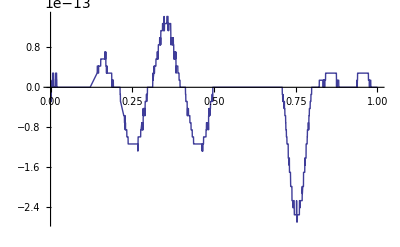

```mathematica
Energy[q_, dq_] := Module[{MM, p},
p = NLink`Private`GetPoints[q]⟦1,All, 2⟧;

NLink`Private`XL = NLink`Private`Xip[q];
NLink`Private`M = NLink`Private`ZM;
NLink`Private`IC = NLink`Private`𝕀;
NLink`Private`JSIM[q];
MM = NLink`Private`M+LowerTriangularize[NLink`Private`M, -1]ᵀ;

1/2 dq.MM.dq +  g Total[inertia⟦;;np, 1⟧ p⟦;;np⟧]
]

Plot[Energy[(flow[s])⟦All,1⟧, (flow'[s])⟦All,1⟧]-Energy[(flow[0])⟦All,1⟧, (flow'[0])⟦All,1⟧], {s, 0, t}, AxesOrigin->{0,0}, PlotRange->All]
```

```mathematica
(* implicit function for time-based passive brachiation *)
root[λ_, opts:OptionsPattern[]]:= Module[{x0, t, M, root, droot},
x0 = λ⟦1;;-2⟧; 
t = λ⟦-1⟧;
M = nlmap[x0, 0, t, opts];
root = FixState[M⟦1⟧ - x0];
droot = M⟦2⟧ - dx0;
(* for passive we only want dxdx0 and dxdt *)
(* also return eigenvalues, since it'll be useful later *)
{root, droot, Eigenvalues[M⟦2, All, ;;-2⟧]}
]

(*MatrixForm /@ root[Append[x0, t]]*)
```

```mathematica
dfdh[x0_, u_, t_, opts:OptionsPattern[]] := Module[{q0, dq0, qimp, x0imp, dx0imp, b, s, df, dh, n},
n = NLink`Private`nq;
q0 = Join[{x0⟦;;n⟧}, dx0⟦;;n⟧ᵀ]ᵀ;
dq0 = Join[{x0⟦n+1;;⟧}, dx0⟦n+1;;⟧ᵀ]ᵀ;
df = fcn[0., q0, dq0];
df⟦All, -1⟧ = df⟦All, 1⟧;
df = Join[dq0, df];

x0imp = Join[PadLeft[x0⟦;;n⟧, n+2], PadLeft[x0⟦n+1;;⟧, n+2]];
dx0imp = Join[ArrayPad[dx0⟦;;n⟧, {{2,0}, {0,0}}], ArrayPad[dx0⟦n+1;;⟧, {{2,0}, {0,0}}]];

qimp =A.h[x0imp, dx0imp]⟦3;;⟧;
dh = Join[{A.x0⟦;;n⟧}, (A.dx0⟦;;n⟧)ᵀ]ᵀ;
dh = Join[dh, qimp];

{df⟦All, 2;;-2⟧, dh⟦All, 2;;-2⟧}
]

{df, dh} =  dfdh[x0, u0, t];
cost[s_Real] := Det[(dh.MatrixExp[df s] - dx0⟦All, ;;-2⟧)];

(*cost[s_Real] := Times@@Abs@Eigenvalues[(dh.MatrixExp[df s] - dx0⟦All, ;;-2⟧), {-1}];*)

Plot[cost[s], {s, 1.2, 1.3}, PlotRange->All]
```

```mathematica
tol = Automatic;10^-8;
t = Chop[s /. First[FindRoot[cost[s] == 0, {s, 1.2}, AccuracyGoal->15,PrecisionGoal->15, MaxIterations->5000]]]
NullSpace[root[Append[x0, t]]⟦2⟧, Tolerance->tol] // Chop // MatrixForm

cost[t]
```

```mathematica
(* example usage *)
m = 250; (* try to generate m points on the curve *)
step = 1/10;

nlroot[root];
Z = nlcurve["nlsln", nlc, Append[x0, t], step, m, Select-> 1];
Beep[]
```

```mathematica
(*DumpSave["HumanWalker3D - 2.mx", Z];*)
```

```mathematica
(*<<"HumanWalker3D - 2.mx";*)
```

```mathematica
scale = 2 torso;

idx = 12;
q0 = Join[{Z⟦idx, 1,;;NLink`Private`nq⟧}, dx0⟦;;NLink`Private`nq⟧ᵀ]ᵀ;
dq0 = Join[{Z⟦idx, 1,NLink`Private`nq+1;;-2⟧}, dx0⟦NLink`Private`nq+1;;⟧ᵀ]ᵀ;
t0 = Z⟦idx, 1,-1⟧;

hw = Module[{q,s},q/. First@NDSolve[{q''[s] == fcn[s, q[s], q'[s]], q[0] == q0, q'[0] == dq0}, q, {s, 0, t0}]];

Animate[
NLink`Private`DrawFigure2D[hw[s]⟦All, 1⟧, poi, VertexColors-> colors, PlotRange->scale{{-1, 1}, {-1,1}}]⟦2⟧,
{s, 0, t0}, AnimationRepetitions->1]
```

```mathematica
Print["q[0]"];
q0 = hw[0][[All, 1]];
g2 = NLink`Private`DrawFigure2D[q0, poi, VertexColors-> colors, PlotRange->scale{{-1, 1}, {-1,1}}]⟦2⟧

Print["q[t0]"];
q0 = hw[t0][[All, 1]];
g6 = NLink`Private`DrawFigure2D[q0, poi, VertexColors-> colors, PlotRange->scale{{-1, 1}, {-1,1}}]⟦2⟧

Print["q[0] & q[t0]"];
Show[g2,g6, PlotRange->All]
```

```mathematica
Animate[NLink`Private`DrawFigure2D[Z⟦i,1⟧, poi, VertexColors-> colors, PlotRange->scale{{-1, 1}, {-1,1}}]⟦2⟧,{i, Range@Length@Z}]
```

```mathematica
x=Interpolation[Table[{{s/hw["Domain"][[1,2]]},hw[s][[All,1]]},{s,hw["Coordinates"][[1]]}]];

lengths={leg,-leg,torso,-arm,-arm};

q2p[q_]:=Module[{p},p=NLink`Private`GetPoints[q][[1]];
p=p[[All,1;;2]];
Table[Join[p[[i]],{A0[[i]].q,lengths[[i]]}],{i,NLink`Private`nq}]];

z=NLink`Private`GetPointsAndLines[x[0],poi][[1,n+1,1;;2]];
z=ArcTan[z[[2]]/z[[1]]];

Show[MotionBlur[x,q2p,{3,5},z&,"stepsize"->1/3,"radius"->1/28],PlotRange->{{-1/2,0.6},{-1,1.3}}]
```